```mathematica
StandardError[data_]:=StandardDeviation[data]/Sqrt[Length[data]]
```

```mathematica
neuroscienceGraph[data_,labels_,plotLabel_]:=Module[{},
listPlotData=MapIndexed[Function[{d,i},Map[{i[[1]],#}&,d]],data];
meanData=Map[Mean,data];
stdevData=Map[StandardError,data];
chartLabels=Placed[Style[#,Bold,FontSize->Scaled[.05],LineSpacing->{0,0}]&/@labels,Below];
errorBar[type_: "Rectangle"][{{x0_,x1_},{y0_,y1_}},value_,meta_]:=Block[{error,mags=QuantityMagnitude[value]},error=Flatten[QuantityMagnitude[meta]];
error=If[error==={},0,Last[error]];{ChartElementData[type][{{x0,x1},{y0,y1}},mags,meta],{Black,Thick,Line[{{{(x0+x1)/2,y1-error},{(x0+x1)/2,y1+error}},{{1/4 (3 x0+x1),y1+error},{1/4 (x0+3 x1),y1+error}},{{1/4 (3 x0+x1),y1-error},{1/4 (x0+3 x1),y1-error}}}]}}];
chartData=Table[meanData[[i]]->stdevData[[i]],{i,1,Length[meanData]}];listPlotCircleMarker=Graphics[{EdgeForm[Thick],White,Disk[]}];
listPlotSquareMarker=Graphics[{EdgeForm[Thick],White,Rectangle[]}];
graph = Show[BarChart[chartData,
ChartElementFunction->errorBar["Rectangle"],
ChartLabels->chartLabels,
ChartStyle->If[Length[chartData]==2,{Directive[Lighter[Red],EdgeForm[{Thickness[0.005],Black}]],Directive[Gray,EdgeForm[{Thickness[0.005],Black}]]},{Directive[Lighter[Lighter[Lighter[Red]]],EdgeForm[{Thickness[0.005],Black}]],Directive[LightGray,EdgeForm[{Thickness[0.005],Black}]],Directive[Lighter[Red],EdgeForm[{Thickness[0.005],Black}]],Directive[Gray,EdgeForm[{Thickness[0.005],Black}]]}],
LabelStyle->Directive[Black,Bold,FontFamily->"Arial",FontSize->16],
AspectRatio->1,
Frame->{True,True,False,False},
FrameStyle->Directive[Bold],
FrameLabel->{None, Rotate["μm^2",3/2π]},
 BarSpacing->Large,
PlotLabel->plotLabel,
ImagePadding->{{80,20},{60,0}}],
ListPlot[listPlotData,
AspectRatio->5,
Axes->None,
PlotStyle->PointSize[Large],
PlotMarkers->{{listPlotCircleMarker,0.03},{listPlotSquareMarker,0.03}}]]]
```

```mathematica
nfhNormal={{461.3,368.418,485.299,574.181},{184.876,164.433,255.537,227.095}};
nfhMutant={{280.869,267.536,253.444,307.556},{282.646,151.989,220.788,195.889}};
zebNormal={{72.55,108.103,152.434,142.656},{480.521,329.643,399.527}};
zebMutant={{353.333,104,135.556,135.556},{234.222,200,319.556,96.444}};
gfp={{542.406,555.183,766.612,897,648.889,312.566}, {233.317,215.429,107.215,345,197.222,196.111}};
labels={"PLCβ4 +","PLCβ4 -",Column[{"PLCβ4 +","Mutant"},Alignment->Center], Column[{"PLCβ4 -","Mutant"},Alignment->Center]};
gfpLabel="PLCβ4 Zones\n";
zebLabel="Zebrin II Zones\n";
zebMutantLabel=StringJoin[zebLabel,"(Mutant)\n"];
nfhLabel="NFH Zones\n";
nfhMutantLabel=StringJoin[nfhLabel,"(Mutant)\n"];
```

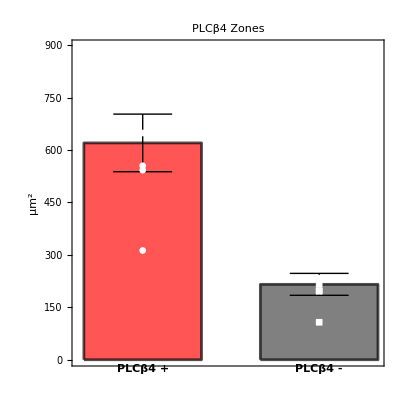

```mathematica
neuroscienceGraph[gfp,labels,gfpLabel]
```